# Calculating H’ ellipse

## Second order approximation for x_1

Calculating the solutions for the ellipse equation H’, as function of spin I and arbitrary energy value E
H'=x^2+uy^2+2 v_0 x_1^2
For specific transformations, the equation can be changed into the following form:
x^2/a_E^2+y^2/b_E^2=1

## Inertial functions

```mathematica
Afct[spin_,j_,a1_,a2_,theta_]:=a2(1-(j*Sin[theta])/spin)-a1;
ufct[spin_,j_,a1_,a2_,a3_,theta_]:=(a3-a1)/Afct[spin,j,a1,a2,theta];
v0fct[spin_,j_,a1_,a2_,theta_]:=-(a1*j*Cos[theta])/Afct[spin,j,a1,a2,theta];
vfct[spin_,j_,a1_,a2_,theta_]:=v0fct[spin,j,a1,a2,theta]/spin;
```

## The ellipse’s (a,b) coefficients

```mathematica
a[I_,E_,j_,a1_,a2_,theta_]:=((1-vfct[I,j,a1,a2,theta])/(E-2*vfct[I,j,a1,a2,theta]*I^2))^(-1/2);
b[I_,E_,j_,a1_,a2_,a3_,theta_]:=((ufct[I,j,a1,a2,a3,theta]-vfct[I,j,a1,a2,theta])/(E-2*vfct[I,j,a1,a2,theta]*I^2))^(-1/2);
```

## Constants

```mathematica
j=5.5;
spinvalue=9/5;
θ=-71*π/180;
```

## MOI Ordering

## 1-axis ordering

```mathematica
A1=1/(2*89);
A2=1/(2*12);
A3=1/(2*48);
```

```mathematica
x2[r_,theta_,fi_]:=r*Sin[theta]Cos[fi];
x3[r_,theta_,fi_]:=r*Sin[theta]Sin[fi];
ae[E_,I_]:=a[I,E,j,A1,A2,θ];
be[E_,I_]:=b[I,E,j,A1,A2,A3,θ];
```

## Test the evolution of (a,b) parameters

## Parameter a

```mathematica
Manipulate[Plot[ae[x,s],{x,0,s},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][s]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],{s,0.5,22.5,2}]
```

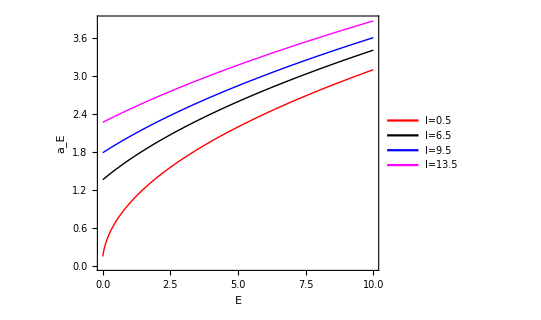

```mathematica
Plot[{ae[x,0.5],ae[x,6.5],ae[x,9.5],ae[x,13.5]},{x,0,10},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick},{Magenta,Thick}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Italic,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I=0.5","I=6.5","I=9.5","I=13.5"},{0.75,0.30}]]
```

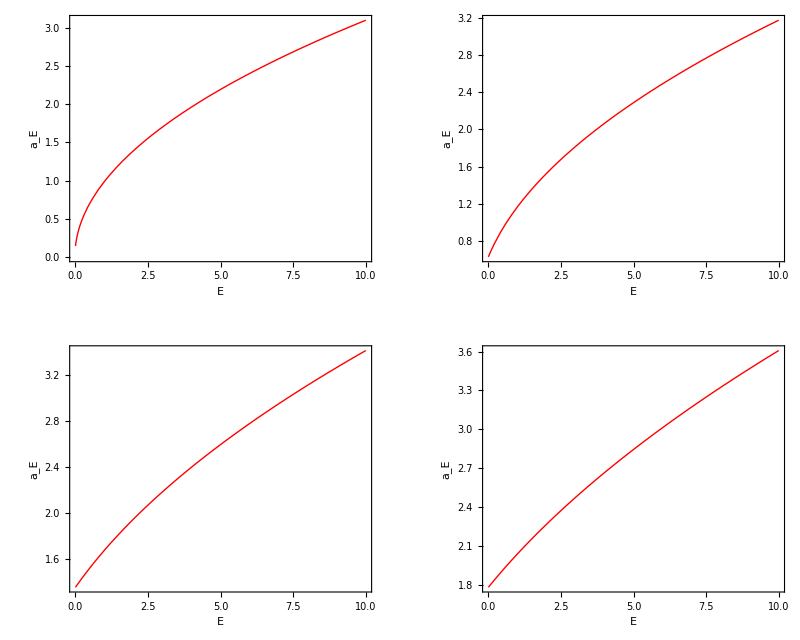

```mathematica
GraphicsGrid[{{Plot[ae[x,0.5],{x,0,10},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][0.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],Plot[ae[x,2.5],{x,0,10},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][2.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.60}]]]}, 
 {Plot[ae[x,6.5],{x,0,10},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][6.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],Plot[ae[x,9.5],{x,0,10},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","a_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][9.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]]}},Frame->All]
```

## Parameter b

```mathematica
Manipulate[Plot[be[x,s],{x,0,s},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][s]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],{s,0.5,22.5,2}]
```

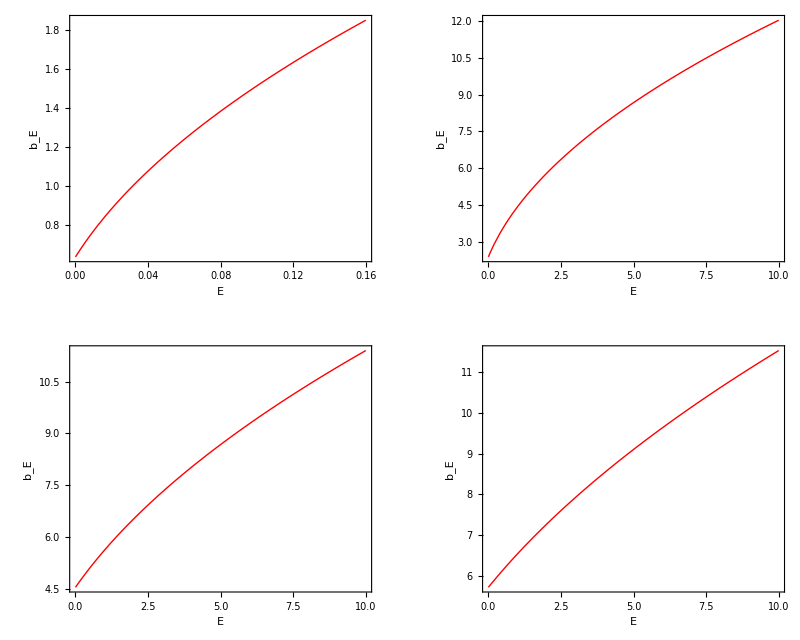

```mathematica
GraphicsGrid[{{Plot[be[x,0.5],{x,0,0.16},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][0.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],Plot[be[x,2.5],{x,0,10},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][2.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.60}]]]}, 
 {Plot[be[x,6.5],{x,0,10},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][6.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],Plot[be[x,9.5],{x,0,10},PlotStyle->{Red,Thick},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``"][9.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]]}},Frame->All]
```

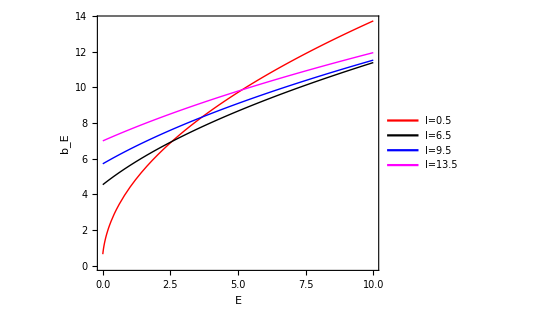

```mathematica
Plot[{be[x,0.5],be[x,6.5],be[x,9.5],be[x,13.5]},{x,0,10},PlotStyle->{{Red,Thick},{Black,Thick},{Blue,Thick},{Magenta,Thick}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"E","b_E"},AspectRatio->0.8,LabelStyle->{18,Bold,Italic,Black,FontFamily->"Times New Roman"},PlotLegends->Placed[{"I=0.5","I=6.5","I=9.5","I=13.5"},{0.75,0.30}]]
```

## Plot the energy ellipse H’ and the angular momentum sphere I

## Intersection points for the ellipse H’ and the am. I

```mathematica
pts[E_,I_]:=NSolve[x^2/ae[E,I]^2+y^2/be[E,I]^2==1&&{x,y}∈Circle[{0,0},I],{x,y}]
intersections[E_,I_]:={Black,PointSize[Large],Point[{x,y}/.pts[E,I]]};
parabola[E_,I_]:=ContourPlot[x^2/ae[E,I]^2+y^2/be[E,I]^2==1,{x,-15,15},{y,-15,15}];
```

```mathematica
Manipulate[Show[ContourPlot[x^2/ae[e,i]^2+y^2/be[e,i]^2==1,{x,-15,15},{y,-15,15},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][i,e]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.70}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},i]}]],{e,0,35,2},{i,2.5,12.5,1}]
```

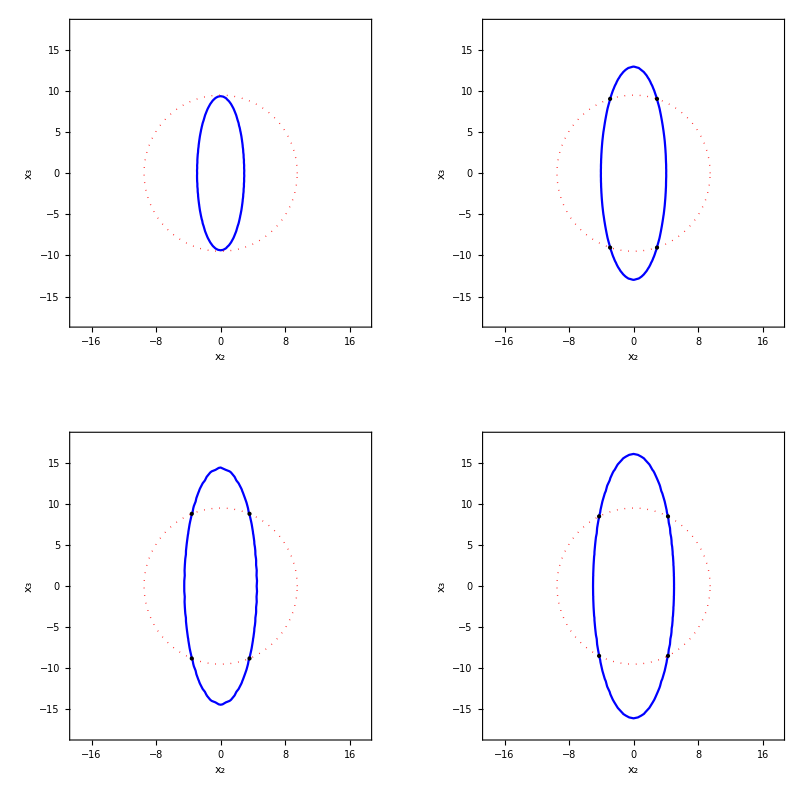

```mathematica
GraphicsGrid[{{Show[ContourPlot[x^2/ae[5.5,9.5]^2+y^2/be[5.5,9.5]^2==1,{x,-18,18},{y,-18,18},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,5.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}]],Show[ContourPlot[x^2/ae[13.5,9.5]^2+y^2/be[13.5,9.5]^2==1,{x,-18,18},{y,-18,18},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,13.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}],Graphics[{intersections[13.5,9.5]}]]},{Show[ContourPlot[x^2/ae[17.5,9.5]^2+y^2/be[17.5,9.5]^2==1,{x,-18,18},{y,-18,18},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,17.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}],Graphics[{intersections[17.5,9.5]}]],Show[ContourPlot[x^2/ae[22.5,9.5]^2+y^2/be[22.5,9.5]^2==1,{x,-18,18},{y,-18,18},AspectRatio->Automatic,ContourStyle->Blue,FrameStyle->Directive[Black,Thick],FrameLabel->{"x_2","x_3"},LabelStyle->{19,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Graphics[Style[Text[TemplateApply[StringTemplate["I=``\n E=``"][9.5,22.5]]],Italic,FontFamily->"Times New Roman",18,Bold]],Scaled[{0.20,0.85}]]],Graphics[{Red,Thick,Dotted,Circle[{0,0},9.5]}],Graphics[{intersections[22.5,9.5]}]]}},Frame->All]
```